Create a function ‘func’ which takes two arguments ‘x’ and ‘y’. The implementation of the function should use Module with one local Symbol called ‘answer’. Define ‘answer’ to be equal to the product x*y and have your function ‘func’ return ‘answer’.

```mathematica
funcxy[x_,y_]:=Module[{answer}, answer= x*y; Return[answer]];
```

```mathematica
(*testing funcxy*)
funcxy[2,3]
```

6

A function ‘func2’ may be defined using predicates (multiple conditional function definitions) as follows:
func2[x_Real,y_Real] /; 3<x<5 := 4 x;
func2[x_Real,y_Real] /; x≤3 := x*y;
func2[x_Real,y_Real] /; 5≤x := y;
Create a new function ‘func3’ which behaves the same as ‘func2’, but implemented using Which instead of conditional function definitions. Create another function ‘func4’ which behaves the same way as ‘func3’, but uses a single Piecewise function instead of Which.

```mathematica
func2[x_Real,y_Real]/; 3<x<5 := 4 x;
func2[x_Real,y_Real]/; x≤ 3 := x * y;
func2[x_Real,y_Real]/; 5≤ x := y;

a=func3[x_Real,y_Real]/; 3<x<5;
b=func3[x_Real,y_Real]/; x≤ 3 ;
c=func3[x_Real,y_Real]/; 5≤ x ;
Which[a, 4x, b, x*y, c, y]
```

```mathematica
p=func3[x_Real,y_Real]/; 3<x<5;
q=func3[x_Real,y_Real]/; x≤ 3 ;
r=func3[x_Real,y_Real]/; 5≤ x ;
Piecewise[{{4x, p},{x*y,q},{y,r}}]
```

Piecewise[{{4 x, func3[x_Real,y_Real]/;3<x<5}, {x y, func3[x_Real,y_Real]/;x≤3}, {y, func3[x_Real,y_Real]/;5≤x}, {0, True}}]

Use Map and Range to make a list of the values of the tangent function evaluated at 1001 equally spaced points between 0 and 2 π . (Make sure that your list is the correct size, with 1001 elements.)

```mathematica
Map[Tan, Subdivide[2 π, 1000]]
```

```mathematica
(*Make sure if length is 1001*)
Map[Tan, Subdivide[2 π, 1000]]//Length
```

1001

Repeat the above using Table instead of Map and Range.

```mathematica
Table[Tan[x], {x, 0, 2 π, (2 π - 0)/1000}]
```

```mathematica
(*Make sure if length is 1001*)
Table[Tan[x], {x, 0, 2 π, (2 π - 0)/1000}]//Length
```

1001

Calculate the sum of the cubes of the first seven perfect numbers (hint: there is a PerfectNumber function) using only the functions Total, PerfectNumber, Range and Power.

```mathematica
Total[Power[PerfectNumber[Range[1,7,1]],3]]
```

2596767384846156628587154386339480

Create a surface plot of the function a Cos[x]+b Sin[y] with -π≤x≤π and -π≤y≤π. Make it so that the parameters -3 ≤a≤4 and -5≤b≤3 can be interactively Manipulated.

```mathematica
Manipulate[Plot3D[a Cos[x] + b Sin[y], {x, -π, π},{y, -π, π}, AxesLabel->{"x","y", "TraditionalForm`a\ Cos[x] + b\ Sin[y]"}, ImageSize->{600,400}, Mesh->All, PlotTheme->"Business", Background->Black], {{a, 0, "A"}, -3, 4},{{b, 0, "B"}, -5, 3}, SynchronousUpdating->True]
```

Solve the following system of equations for x and y (the solution will be somewhat complicated):
5 x^2+2x y-3 y^2=0
cos (x^3+27x y)=0
Explain in 1-2 sentences why C[1] appears in your solution and determine numerical values for the the solution when C[1]=0.

```mathematica
Clear[x,y];
Solve[5 x^2+2 x y - 3 y^2==0, Cos[x^3+27 x y]==0,x, y]
```

Solve::bddom: Value y of the domain argument should be Complexes, Reals, Algebraics, Rationals, Integers, Primes, or Automatic.

Solve[5 x^2+2 x y-3 y^2==0,Cos[x^3+27 x y]==0,x,y]

Create plots of the function f(x)=ⅇ^x-x^5 over the range x ∈[-10,20] using: (i) a linear scale and (ii) a logarithmic scale. Note that you will need to plot the absolute value, |f(x)|, in the latter case.

```mathematica
func[x_]:= ⅇ^x-x^5;
```

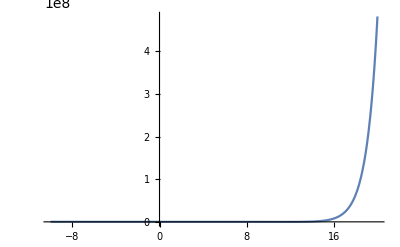

```mathematica
Plot[func[x],{x, -10,20}, PlotRange->All]
```

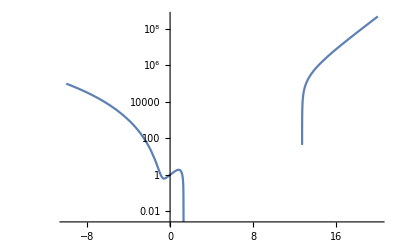

```mathematica
LogPlot[func[x],{x, -10,20}, PlotRange->All]
```

Determine the analytic solutions to f(x)=0 using both Reduce and Solve. Briefly explain (1-2 sentences) the difference between the two solutions.

```mathematica
Solve[func[x]==0, x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-5 ProductLog[-1/5]},{x→-5 ProductLog[1/5 (-1)^(1/5)]},{x→-5 ProductLog[-1/5 (-1)^(2/5)]},{x→-5 ProductLog[1/5 (-1)^(3/5)]},{x→-5 ProductLog[-1/5 (-1)^(4/5)]},{x→-5 ProductLog[-1,-1/5]}}

```mathematica
Reduce[func[x]==0, x]
```

C[1]∈ℤ&&(x==-5 ProductLog[C[1],-1/5]||x==-5 ProductLog[C[1],1/5 (-1)^(1/5)]||x==-5 ProductLog[C[1],-1/5 (-1)^(2/5)]||x==-5 ProductLog[C[1],1/5 (-1)^(3/5)]||x==-5 ProductLog[C[1],-1/5 (-1)^(4/5)])

Solve gives list of roots whereas Reduce gives generic solution which is exactly satisfied by x.

Use FindRoot to determine the two real valued numerical solutions to f(x)=0.

```mathematica
Block[{$RecursionLimit=1000},FindRoot[func[x], {x, -10,20}]]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{x→15.208}